```mathematica
Remove["Global`*"]
```

# SWAP FOC5-3rd run

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[!OptionValue[ignoreCell][position],If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[OptionValue[borderDirectives]],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow=Append[OptionValue[arrowDirectives],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics[frame~Join~centralPoint~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}]];
```

```mathematica
lowerTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]>-#[[2]]&)]
upperTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]<-#[[2]]&)]
diagonalComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]!=-#[[2]]&)]
```

### matrixDraw3D

```mathematica
Options[myPlotElement3D]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
showBar->True,whatBarShape->"circle",barLengthFunction->Abs,barDiameter->0.99,hideBarSmallerThan->0,barDirectives->{Opacity[1]},barColorFunction->(Hue[#2/(2π )+0.5]&),
showArrow->True,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},arrowLength->(1/2&),
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}};

myPlotElement3D[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],φ=Arg[c],frame={},bar={},arrow={},centralPoint={},number={},val=OptionValue[barLengthFunction][c]},
If[!OptionValue[ignoreCell][position],
If[OptionValue[showFrame],
frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Polygon[{Append[center+{-0.5,-0.5},0],Append[center+{0.5,-0.5},0],Append[center+{0.5,0.5},0],Append[center+{-0.5,0.5},0]}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[Append[center,0]]}];
If[OptionValue[showBar] &&Abs[val]>OptionValue[hideBarSmallerThan],
bar=Append[OptionValue[barDirectives],OptionValue[barColorFunction][val,Arg[c]]];
bar=Append[bar,
Switch[OptionValue[whatBarShape],
"square",Cuboid[Append[center-OptionValue[barDiameter]{0.5,0.5},0],Append[center+OptionValue[barDiameter]{0.5,0.5},val]],
_,Cylinder[{Append[center,0],Append[center,val]},OptionValue[barDiameter]/2]]]];
If[OptionValue[showArrow] && Abs[val]>OptionValue[hideArrowSmallerThan],
arrow=OptionValue[arrowDirectives];
AppendTo[arrow,Arrow[{Append[center,val],Append[center,val]+OptionValue[arrowLength][val]{ Cos[Arg[c]], Sin[Arg[c]],0}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics3D[frame~Join~centralPoint~Join~bar~Join~arrow~Join~centralPoint~Join~number,Lighting->{{"Ambient",White}}]];

matrixDraw3D[number_?NumberQ,opts___]:=matrixDraw3D[{{number}},opts];
matrixDraw3D[vector_?VectorQ,opts___]:=matrixDraw3D[List/@vector,opts];
matrixDraw3D[matrix_,opts___]:=Show[MapIndexed[myPlotElement3D[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}],BoxRatios->{1,1,1}];
```

### Definitions of the concurence conc[ρ] of a density matrix ρ

```mathematica
(σyy=KroneckerProduct[σy,σy]);
conc[ρ_]:=Block[{ρt=σyy.Conjugate[ρ].σyy},Max[0,Plus@@((Eigenvalues[ρ.ρt]//Chop//Sqrt//Sort//Reverse){1,-1,-1,-1})]]
```

### Density matrices SWAP

#### Ideal density matrices

```mathematica
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
```

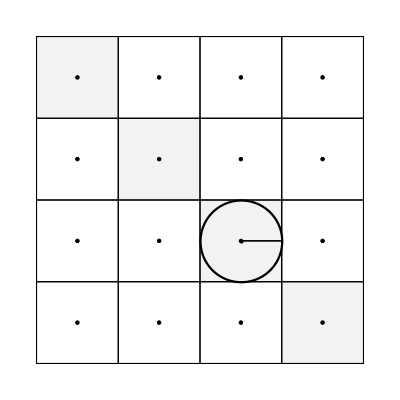
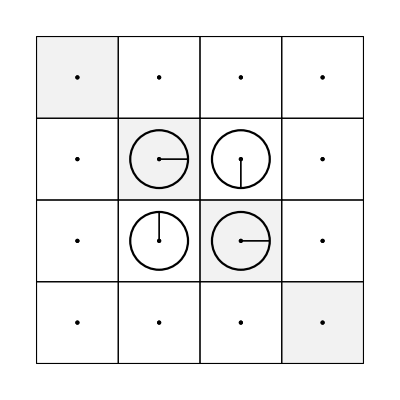

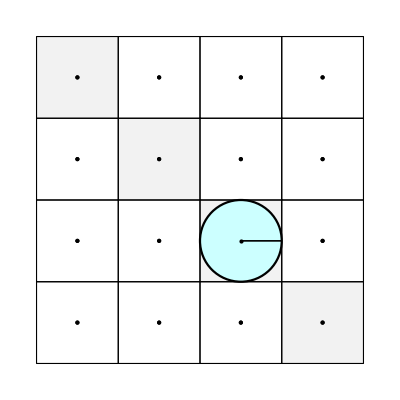
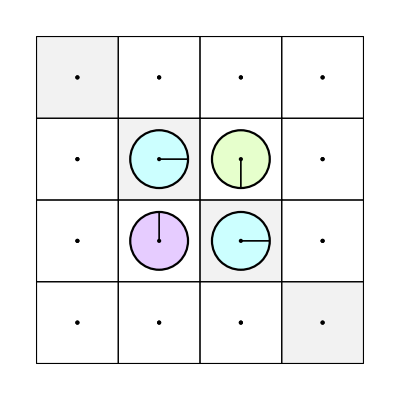

```mathematica
idealState3=Table[0,{i,1,4},{j,1,4}]/2;idealState3[[3,3]]=1;
idealStatehalfSWAP={{0,0,0,0},{0,1,-I,0},{0,I,1,0},{0,0,0,0}}/2;
idealMatrices={idealState3,idealStatehalfSWAP};
opts0={
borderDirectives->{Black,Thickness[0.004]},arrowDirectives->{Black,Thickness[0.003],Arrowheads[0]},fill2DShape->False,hide2DShapeSmallerThan->0.01,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&),frameFaceFunction->(GrayLevel[1-0.05KroneckerDelta[#1,-#2]]&),
showCentralPoint->True ,centralPointSize->Small};
opts0b={
borderDirectives->{Black,Thickness[0.004]},
arrowDirectives->{Black,Thickness[0.003],Arrowheads[0]},
hide2DShapeSmallerThan->0.01,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&),frameFaceFunction->(GrayLevel[1-0.05KroneckerDelta[#1,-#2]]&),
showCentralPoint->True ,centralPointSize->Small,
fillingColor->(Hue[#2/(2π)+0.5,0.2,1]&)};
idealGraphs=complexMatrixDraw[#,Sequence @@ opts0]&/@idealMatrices
idealGraphsb=complexMatrixDraw[#,Sequence @@ opts0b]&/@idealMatrices
```

```mathematica
opts0={
borderDirectives->{Black,Thickness[0.004]},arrowDirectives->{Black,Thickness[0.003],Arrowheads[0]},fill2DShape->False,hide2DShapeSmallerThan->0.01,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&),frameFaceFunction->(GrayLevel[1-0.05KroneckerDelta[#1,-#2]]&),
showCentralPoint->True ,centralPointSize->Small};
idealGraphs=complexMatrixDraw[#,Sequence @@ opts0]&/@idealMatrices
```

#### Import reconstructed density matrices

The density matrices are reconstructed as ρListExp4P in the "QProcessTomography14.nb" Mathematica file. Note that it includes a correction of the tomographic pulse errors

```mathematica
myρs={{{{0.9809531272055346,0.035423467936811726-0.005043443853070051 ⅈ,0.041767833264230246-0.008379703151069734 ⅈ,0.006097845651405361-0.019285136727821756 ⅈ},{0.035423467936811726+0.00504344385307005 ⅈ,0.006638867010913383,-0.003630386788559219+0.0026783822203989846 ⅈ,-0.00018588497137358144+0.00011626500296183808 ⅈ},{0.041767833264230246+0.008379703151069732 ⅈ,-0.00363038678855922-0.0026783822203989846 ⅈ,0.010282453171719979,-0.0002675719847352412-0.00054880930843386 ⅈ},{0.00609784565140536+0.01928513672782176 ⅈ,-0.00018588497137358154-0.00011626500296183797 ⅈ,-0.00026757198473524124+0.00054880930843386 ⅈ,0.002125552611832508}},{{0.018340145168549336,-0.007970715395594876+0.033907906407898473 ⅈ,-0.0012003928923482567+0.0017551660033681973 ⅈ,-0.0051144044906827205+0.007597437988486566 ⅈ},{-0.007970715395594876-0.033907906407898473 ⅈ,0.974195114757916,0.007429671048646536-0.012143237158091636 ⅈ,0.03751716358658327+0.013486542970340385 ⅈ},{-0.0012003928923482567-0.001755166003368197 ⅈ,0.007429671048646536+0.012143237158091636 ⅈ,0.0008686687829012323,0.0005692803240308676-0.0002702636210139405 ⅈ},{-0.0051144044906827205-0.007597437988486567 ⅈ,0.03751716358658327-0.013486542970340385 ⅈ,0.0005692803240308676+0.0002702636210139404 ⅈ,0.006596071290633332}},{{0.5058322197261426,0.4820792054755712+0.0275305930713266 ⅈ,0.02594064428171056+0.00166281363619194 ⅈ,0.024954447764195496-0.00843650791660765 ⅈ},{0.4820792054755712-0.027530593071326596 ⅈ,0.486520397624216,0.02464312791814379-0.0085851968995236 ⅈ,0.016322368349555326-0.008614817322062394 ⅈ},{0.02594064428171056-0.00166281363619194 ⅈ,0.024643127918143794+0.008585196899523601 ⅈ,0.004335449129947418,0.0010301845085558614-0.002916880851109774 ⅈ},{0.024954447764195493+0.008436507916607648 ⅈ,0.016322368349555333+0.008614817322062394 ⅈ,0.0010301845085558614+0.002916880851109774 ⅈ,0.003311933519693878}},{{0.4574088796116301,-0.008196968258433563-0.4903542463920161 ⅈ,0.010366244440514717-0.0009196426082903786 ⅈ,0.00034859209945595476-0.031796741464174015 ⅈ},{-0.008196968258433563+0.4903542463920161 ⅈ,0.5357047751103856,-0.003357506242794819+0.010425264074274444 ⅈ,0.02964138456977707+0.0034716708581501326 ⅈ},{0.010366244440514717+0.0009196426082903788 ⅈ,-0.003357506242794819-0.010425264074274444 ⅈ,0.0020355588482525596,0.0017588579420534808-0.0020994089274915624 ⅈ},{0.00034859209945595476+0.03179674146417402 ⅈ,0.02964138456977707-0.0034716708581501326 ⅈ,0.0017588579420534808+0.0020994089274915624 ⅈ,0.004850786429731628}},{{0.03607516341600852,0.008265232801347782-0.004330371986804615 ⅈ,0.05524408703572831-0.0038098897848449064 ⅈ,0.00906250471936445-0.012106058166064068 ⅈ},{0.00826523280134778+0.004330371986804615 ⅈ,0.00410549479080171,0.032532939227718834+0.012423279083661526 ⅈ,0.0007307759922037717-0.0008621245378276569 ⅈ},{0.05524408703572832+0.0038098897848449064 ⅈ,0.03253293922771884-0.012423279083661526 ⅈ,0.9480531914326946,-0.028058763134244418-0.003265343545633366 ⅈ},{0.009062504719364449+0.012106058166064066 ⅈ,0.0007307759922037715+0.0008621245378276567 ⅈ,-0.028058763134244415+0.003265343545633366 ⅈ,0.011766150360495286}},{{0.0035221584360167345,0.006795918621586598-0.007879467087344164 ⅈ,0.000012569909366304298-0.0031183637566123937 ⅈ,0.00951990608650201+0.0022115150287959993 ⅈ},{0.006795918621586598+0.007879467087344164 ⅈ,0.03512356990082366,0.005901139079022237-0.0033777701416823546 ⅈ,0.06687569071086018+0.014513586998695486 ⅈ},{0.000012569909366304095+0.0031183637566123946 ⅈ,0.005901139079022237+0.003377770141682355 ⅈ,0.036161786950354824,0.03451708143678867+0.04028794528012537 ⅈ},{0.00951990608650201-0.0022115150287959993 ⅈ,0.06687569071086018-0.014513586998695486 ⅈ,0.034517081436788666-0.04028794528012537 ⅈ,0.9251924847128047}},{{0.026666735636813668,0.020420988123402727-0.0007881977284122122 ⅈ,0.03398132421059875+0.009698739049990884 ⅈ,0.0399176012578737+0.0032766668850817146 ⅈ},{0.020420988123402727+0.0007881977284122121 ⅈ,0.017557420525757116,0.029640061909234124+0.014841181442718388 ⅈ,0.027698301204532833+0.006855910568573247 ⅈ},{0.03398132421059875-0.009698739049990884 ⅈ,0.029640061909234124-0.014841181442718388 ⅈ,0.5145883185895546,0.46033374602635946-0.007965698595664051 ⅈ},{0.0399176012578737-0.003276666885081713 ⅈ,0.02769830120453283-0.0068559105685732456 ⅈ,0.46033374602635946+0.007965698595664051 ⅈ,0.4411875252478752}},{{0.020488128770911974,0.008095980307505796-0.012792797023405184 ⅈ,0.01467813243819909+0.007847824142529675 ⅈ,0.00690077917871017-0.025387061729371895 ⅈ},{0.008095980307505796+0.012792797023405184 ⅈ,0.012978545589154697,0.004046034618004931+0.01819573799684914 ⅈ,0.02161422225840252-0.0021145239722281466 ⅈ},{0.014678132438199086-0.007847824142529675 ⅈ,0.004046034618004931-0.01819573799684914 ⅈ,0.44947694939269045,-0.008172186247367489-0.4638659730515591 ⅈ},{0.006900779178710168+0.02538706172937189 ⅈ,0.02161422225840252+0.002114523972228146 ⅈ,-0.008172186247367489+0.4638659730515591 ⅈ,0.5170563762472431}},{{0.5566976778512622,0.016868392364505606-0.005204113314307634 ⅈ,0.49609836277161556-0.01836082708395127 ⅈ,0.004227423999682722-0.0022740361400144372 ⅈ},{0.016868392364505606+0.005204113314307634 ⅈ,0.0005597750246666643,0.015203824258758856+0.004081271666673075 ⅈ,0.00014935249737732157-0.000029386399458320933 ⅈ},{0.49609836277161556+0.01836082708395127 ⅈ,0.015203824258758856-0.004081271666673075 ⅈ,0.44270115597954873,0.0038422493831651683-0.0018870684155370319 ⅈ},{0.004227423999682722+0.0022740361400144372 ⅈ,0.00014935249737732157+0.000029386399458320933 ⅈ,0.0038422493831651683+0.0018870684155370319 ⅈ,0.000041391144522326626}},{{0.009135035383606903,-0.005166864993896848+0.012684552417428708 ⅈ,0.005375117332399929+0.0011252437196321932 ⅈ,-0.005882443678878482+0.012146644162574044 ⅈ},{-0.005166864993896849-0.01268455241742871 ⅈ,0.5395207976108937,0.0065077618245349255-0.014653609892358406 ⅈ,0.49143161802291996+0.004017819560473721 ⅈ},{0.005375117332399929-0.0011252437196321932 ⅈ,0.0065077618245349255+0.014653609892358406 ⅈ,0.0035069875544279884,0.005251432592273627+0.01386417128573478 ⅈ},{-0.005882443678878481-0.012146644162574044 ⅈ,0.4914316180229199-0.00401781956047372 ⅈ,0.005251432592273628-0.013864171285734778 ⅈ,0.447837179451071}},{{0.29580287531736965,0.2728577158797777+0.013252915792998657 ⅈ,0.2609043216683949-0.007055875531065195 ⅈ,0.2421532082869118+0.004917240218658363 ⅈ},{0.2728577158797777-0.013252915792998653 ⅈ,0.26086919759645816,0.24621361804570144-0.02107937635174275 ⅈ,0.22852287726044082-0.012500508204921544 ⅈ},{0.26090432166839483+0.007055875531065194 ⅈ,0.24621361804570144+0.02107937635174275 ⅈ,0.23672312665852957,0.21807396542251176+0.006679883398512067 ⅈ},{0.2421532082869118-0.004917240218658363 ⅈ,0.22852287726044082+0.012500508204921544 ⅈ,0.21807396542251176-0.006679883398512067 ⅈ,0.20660480042764295}},{{0.2678301985891403,0.0017607293383926543-0.2767891963312616 ⅈ,0.22927792915931652+0.006657627283298587 ⅈ,0.005441021281588512-0.2517659605387922 ⅈ},{0.0017607293383926548+0.27678919633126164 ⅈ,0.28814073315098243,-0.0013941178470472078+0.23732727722282226 ⅈ,0.2623512864120316+0.005393266254951847 ⅈ},{0.22927792915931652-0.006657627283298587 ⅈ,-0.0013941178470472078-0.23732727722282224 ⅈ,0.20410154661119825,0.0026978082610619727-0.21328001445473055 ⅈ},{0.005441021281588514+0.2517659605387922 ⅈ,0.26235128641203154-0.005393266254951847 ⅈ,0.0026978082610619727+0.21328001445473058 ⅈ,0.239927521648679}},{{0.474411345077288,0.015192484295673462-0.002729274167214047 ⅈ,0.029823946847038645-0.48299428421973317 ⅈ,0.016824653294107227-0.010886740510785746 ⅈ},{0.015192484295673464+0.002729274167214047 ⅈ,0.001077226973662624,0.0009023936228601422-0.012447861318058265 ⅈ,0.001424204653761728-0.0009440764012587174 ⅈ},{0.02982394684703864+0.48299428421973317 ⅈ,0.0009023936228601422+0.012447861318058261 ⅈ,0.5216542285185679,0.004661450556183158+0.015778099400822164 ⅈ},{0.01682465329410723+0.010886740510785746 ⅈ,0.0014242046537617278+0.0009440764012587174 ⅈ,0.004661450556183158-0.015778099400822164 ⅈ,0.002857199430481785}},{{0.006822356948348334,-0.0003004594581782283+0.002883645058195689 ⅈ,-0.0006352298089958968-0.0067665495893716255 ⅈ,0.0011650859424902338-0.0017535178081935332 ⅈ},{-0.00030045945817822875-0.0028836450581956894 ⅈ,0.46078177763790124,-0.001946747525517348-0.015024909998529302 ⅈ,-0.003118157885675041-0.4794471685551994 ⅈ},{-0.0006352298089958966+0.0067665495893716255 ⅈ,-0.0019467475255173475+0.015024909998529304 ⅈ,0.01462239737214863,0.022138473240024475-0.0037304395986298435 ⅈ},{0.0011650859424902332+0.0017535178081935332 ⅈ,-0.003118157885675041+0.4794471685551994 ⅈ,0.022138473240024475+0.0037304395986298435 ⅈ,0.5177734680416018}},{{0.23491271829904156,0.22163644163718796+0.022057851043391606 ⅈ,0.006597308715177262-0.2459068637825758 ⅈ,0.019494730071902118-0.22579941166331396 ⅈ},{0.221636441637188-0.022057851043391606 ⅈ,0.23328921463612295,-0.011625013253580006-0.24601807164635342 ⅈ,-0.007868513262922162-0.23662078771749787 ⅈ},{0.006597308715177263+0.24590686378257584 ⅈ,-0.011625013253580008+0.24601807164635342 ⅈ,0.28445073942286925,0.2583036742224898+0.01016112957839819 ⅈ},{0.01949473007190212+0.225799411663314 ⅈ,-0.007868513262922162+0.23662078771749787 ⅈ,0.2583036742224898-0.01016112957839819 ⅈ,0.24734732764196637}},{{0.22257990683025022,0.003457030435561656-0.23050908671087625 ⅈ,-0.02130074900704422-0.23398817593630394 ⅈ,-0.2397110467114847+0.009041684245196233 ⅈ},{0.003457030435561656+0.23050908671087625 ⅈ,0.24250188259168357,0.2380663716648939-0.025165722142632206 ⅈ,-0.014633427049717993-0.25305574841624856 ⅈ},{-0.02130074900704422+0.23398817593630394 ⅈ,0.2380663716648939+0.02516572214263221 ⅈ,0.25839405467871096,0.006328701405242895-0.2488330178442602 ⅈ},{-0.2397110467114847-0.009041684245196233 ⅈ,-0.014633427049717993+0.25305574841624856 ⅈ,0.006328701405242893+0.24883301784426015 ⅈ,0.27652415589935564}}},{{{0.995207411944162,0.03947095682308105-0.008001078871625952 ⅈ,0.04870025531590167-0.0223981568577429 ⅈ,0.008941049624386759-0.013939540633810537 ⅈ},{0.03947095682308105+0.008001078871625952 ⅈ,0.001629784581759638,0.0021115750035860218-0.0004968030708612297 ⅈ,0.0004666797515256108-0.0004809740738523923 ⅈ},{0.04870025531590167+0.0223981568577429 ⅈ,0.0021115750035860218+0.0004968030708612297 ⅈ,0.002887229600556152,0.0007512518578214726-0.00048090091587856226 ⅈ},{0.008941049624386759+0.013939540633810537 ⅈ,0.0004666797515256108+0.0004809740738523923 ⅈ,0.0007512518578214726+0.00048090091587856226 ⅈ,0.0002755738735221449}},{{0.07252527035737798,0.03468319109535031+0.011180407974293708 ⅈ,-0.0488013378591014+0.05616777726688636 ⅈ,-0.008343307363943153-0.019991433396617974 ⅈ},{0.03468319109535031-0.011180407974293712 ⅈ,0.4181865296813704,0.03799610553140978+0.44373987697915634 ⅈ,0.0067426050751420025-0.009572444943634644 ⅈ},{-0.0488013378591014-0.05616777726688637 ⅈ,0.03799610553140978-0.44373987697915634 ⅈ,0.502336333164985,-0.009377734881464244+0.00560060713509918 ⅈ},{-0.008343307363943153+0.019991433396617974 ⅈ,0.0067426050751420025+0.009572444943634642 ⅈ,-0.009377734881464242-0.00560060713509918 ⅈ,0.006951866796266995}},{{0.5432758988878639,0.32503666721426144+0.09515900684140731 ⅈ,-0.07602526921280897+0.35618781028567037 ⅈ,0.020206630508627615-0.01911071132000978 ⅈ},{0.32503666721426144-0.09515900684140731 ⅈ,0.21113410672479196,0.016903893888171748+0.22642010831430484 ⅈ,0.008742039793467195-0.014973100818597419 ⅈ},{-0.07602526921280897-0.35618781028567037 ⅈ,0.016903893888171748-0.22642010831430484 ⅈ,0.24416617417876776,-0.0153572373805968-0.010573740732705266 ⅈ},{0.020206630508627615+0.01911071132000978 ⅈ,0.008742039793467195+0.014973100818597419 ⅈ,-0.0153572373805968+0.010573740732705266 ⅈ,0.0014238202085762174}},{{0.5290445972641709,0.053502035101980844-0.32297314512433734 ⅈ,0.33002020987531283+0.026553548501899712 ⅈ,-0.007069798502955472-0.019040955588799473 ⅈ},{0.053502035101980844+0.3229731451243373 ⅈ,0.23247579649230288,0.025351590480965542+0.22917433794102451 ⅈ,-0.0028344696322768967-0.0007637038172196653 ⅈ},{0.33002020987531283-0.02655354850189971 ⅈ,0.02535159048096555-0.22917433794102454 ⅈ,0.23037771408406865,-0.004545780344685428+0.00147824093297049 ⅈ},{-0.007069798502955472+0.019040955588799473 ⅈ,-0.0028344696322768967+0.0007637038172196653 ⅈ,-0.004545780344685428-0.0014782409329704908 ⅈ,0.008101892159457814}},{{0.07456964319740175,-0.03529933314146012+0.06391369878227601 ⅈ,0.03865762155257399+0.026561141182035782 ⅈ,0.01893297042406667+0.018128839322541373 ⅈ},{-0.03529933314146012-0.06391369878227601 ⅈ,0.5018214152108191,-0.014767161790399231-0.4513085120310012 ⅈ,-0.01332943744606598-0.0060294973304284285 ⅈ},{0.03865762155257399-0.02656114118203578 ⅈ,-0.014767161790399231+0.45130851203100114 ⅈ,0.41265429039914614,-0.000538455061837514-0.0169463770871766 ⅈ},{0.01893297042406667-0.018128839322541373 ⅈ,-0.013329437446065979+0.0060294973304284285 ⅈ,-0.0005384550618375153+0.0169463770871766 ⅈ,0.010954651192632994}},{{0.01686156516399881,0.0012066618602121519+0.005599043801405681 ⅈ,0.0009496311785866648+0.010265447078087011 ⅈ,0.0006125000674753718+0.005261646041468516 ⅈ},{0.0012066618602121519-0.005599043801405681 ⅈ,0.08829068983099908,0.001043694252426072-0.0168335860230608 ⅈ,-0.0023591425702007497-0.0014841198831695495 ⅈ},{0.0009496311785866648-0.010265447078087013 ⅈ,0.0010436942524260728+0.016833586023060808 ⅈ,0.09314341209249921,0.04606096981129366-0.04469654855635772 ⅈ},{0.0006125000674753718-0.005261646041468516 ⅈ,-0.0023591425702007493+0.0014841198831695487 ⅈ,0.04606096981129366+0.04469654855635772 ⅈ,0.8017043329125029}},{{0.06258107646760003,0.004693447555709496+0.042331437749696964 ⅈ,0.010645489297863738+0.04586824955239244 ⅈ,0.023935844480225555+0.05942398495810816 ⅈ},{0.004693447555709489-0.042331437749696964 ⅈ,0.28047617648439005,-0.0024869779952039718-0.22922901176331634 ⅈ,0.013943808555811829-0.28414741802596827 ⅈ},{0.010645489297863742-0.04586824955239244 ⅈ,-0.0024869779952039726+0.22922901176331634 ⅈ,0.2574765529908961,0.2813873493703236-0.013827077177296018 ⅈ},{0.023935844480225555-0.05942398495810816 ⅈ,0.013943808555811829+0.2841474180259683 ⅈ,0.2813873493703236+0.013827077177296018 ⅈ,0.39946619405711414}},{{0.036576446356353626,-0.026106059569328155+0.01481879733377901 ⅈ,0.02895698270203126+0.022859881531824625 ⅈ,0.04409273246007049-0.0036700933429914644 ⅈ},{-0.026106059569328155-0.01481879733377901 ⅈ,0.254123335984484,-0.005074412402730509-0.24314161269836349 ⅈ,-0.3417819352350278+0.0013341714641660685 ⅈ},{0.028956982702031252-0.022859881531824625 ⅈ,-0.005074412402730509+0.24314161269836346 ⅈ,0.23899031538481738,0.008554093939413024-0.31946120939418626 ⅈ},{0.04409273246007049+0.0036700933429914644 ⅈ,-0.3417819352350278-0.0013341714641660685 ⅈ,0.008554093939413025+0.3194612093941863 ⅈ,0.4703099022743447}},{{0.5775831198493082,-0.030843124326964046+0.35277412999945756 ⅈ,0.3436423995617372+0.00842005108110747 ⅈ,0.018313030816271957-0.009143919558385245 ⅈ},{-0.030843124326964046-0.35277412999945756 ⅈ,0.21711314061228093,-0.013207846276741169-0.2103382959847373 ⅈ,-0.006562811867239369-0.01069687851629129 ⅈ},{0.3436423995617372-0.00842005108110747 ⅈ,-0.013207846276741169+0.2103382959847373 ⅈ,0.20457834028734315,0.010762332501701898-0.005707291297269824 ⅈ},{0.018313030816271957+0.009143919558385245 ⅈ,-0.006562811867239369+0.01069687851629129 ⅈ,0.010762332501701898+0.005707291297269824 ⅈ,0.000725399251067549}},{{0.06105528396024886,0.0024253591855691817+0.03824374333859583 ⅈ,-0.004866944815710535+0.029261093031937066 ⅈ,0.004316706756822358+0.02260106789343455 ⅈ},{0.0024253591855691817-0.03824374333859583 ⅈ,0.2892673850072501,0.016450700348889832+0.21295858475372859 ⅈ,0.2859684135499287+0.0004220958448834843 ⅈ},{-0.004866944815710535-0.029261093031937066 ⅈ,0.016450700348889832-0.21295858475372859 ⅈ,0.26563325888325,0.02608130958081621-0.2962000337655041 ⅈ},{0.004316706756822358-0.022601067893434554 ⅈ,0.2859684135499287-0.0004220958448834843 ⅈ,0.026081309580816215+0.2962000337655041 ⅈ,0.3840440721492508}},{{0.33498658385368185,0.16244497158558968+0.24157374156619704 ⅈ,0.16329386772815366+0.16654901847916992 ⅈ,0.23583506085632755+0.027641136087007398 ⅈ},{0.16244497158558965-0.24157374156619704 ⅈ,0.2624845766027013,0.21852419818042745-0.03962707107956459 ⅈ,0.1273485791949571-0.1727036389700376 ⅈ},{0.16329386772815363-0.1665490184791699 ⅈ,0.21852419818042745+0.03962707107956456 ⅈ,0.20206686570227186,0.1190831725366599-0.138167388007718 ⅈ},{0.23583506085632752-0.027641136087007398 ⅈ,0.1273485791949571+0.1727036389700376 ⅈ,0.1190831725366599+0.138167388007718 ⅈ,0.20046197384134543}},{{0.3324261482270485,0.03418264499423916+0.005076938735362231 ⅈ,0.34011598367219725+0.044054476862759186 ⅈ,0.060748928110478106-0.21106694360879574 ⅈ},{0.034182644994239154-0.005076938735362229 ⅈ,0.03624603379843129,0.031713986744319085-0.027623619825910634 ⅈ,-0.026876475014356763-0.0011939322313271397 ⅈ},{0.3401159836721972-0.044054476862759186 ⅈ,0.031713986744319085+0.027623619825910634 ⅈ,0.40093097457259336,0.011885431420062063-0.2829100937282749 ⅈ},{0.06074892811047809+0.21106694360879577 ⅈ,-0.026876475014356756+0.0011939322313271432 ⅈ,0.011885431420062065+0.2829100937282749 ⅈ,0.23039684340192626}},{{0.5207085211163487,0.36079200032066244+0.07666731768085883 ⅈ,0.04103806787257685-0.33357312596752 ⅈ,0.020197907543994767+0.012621537378547388 ⅈ},{0.36079200032066244-0.07666731768085883 ⅈ,0.26127620267109763,-0.020679420029888186-0.2371706798514996 ⅈ,0.01585321258660005+0.005771425282845646 ⅈ},{0.04103806787257685+0.33357312596752 ⅈ,-0.020679420029888186+0.2371706798514996 ⅈ,0.21692587849396483,-0.006493695493890195+0.013933789002521823 ⅈ},{0.020197907543994767-0.012621537378547388 ⅈ,0.01585321258660005-0.005771425282845646 ⅈ,-0.006493695493890195-0.013933789002521823 ⅈ,0.0010893977185886681}},{{0.058054265774443066,0.046400229129430835+0.002802742669710751 ⅈ,-0.022209186681312738-0.0032389081256575802 ⅈ,0.0373732617991486-0.02090771048726763 ⅈ},{0.04640022912943083-0.0028027426697107543 ⅈ,0.25153836251116035,0.041587051123563853+0.22616108186009787 ⅈ,0.013003160555454335-0.2832704910576629 ⅈ},{-0.022209186681312745+0.0032389081256575802 ⅈ,0.041587051123563853-0.22616108186009787 ⅈ,0.2684894659042254,-0.30661736561275443-0.041336506861171865 ⅈ},{0.0373732617991486+0.020907710487267625 ⅈ,0.013003160555454335+0.28327049105766283 ⅈ,-0.30661736561275443+0.041336506861171865 ⅈ,0.42191790581017113}},{{0.2855023140189987,0.34290779173295927+0.0687427977407492 ⅈ,-0.019429674902696065+0.0005361238499821362 ⅈ,0.060802264095435245-0.21366500004673358 ⅈ},{0.34290779173295927-0.0687427977407492 ⅈ,0.4560972188421591,-0.012472400891592987+0.013999798682416978 ⅈ,0.012535721872806662-0.3002168055390106 ⅈ},{-0.019429674902696065-0.0005361238499821397 ⅈ,-0.012472400891592992-0.013999798682416981 ⅈ,0.045098833029499574,-0.023462272434109893+0.02108232195458548 ⅈ},{0.06080226409543524+0.21366500004673356 ⅈ,0.012535721872806662+0.3002168055390106 ⅈ,-0.023462272434109893-0.02108232195458548 ⅈ,0.21330163410934222}},{{0.2828864799527876,0.22840116713461653-0.12697840637118032 ⅈ,0.19021805114220836-0.13397749320695798 ⅈ,-0.1887506490002207-0.044288883288470526 ⅈ},{0.2284011671346165+0.1269784063711803 ⅈ,0.27337856161860624,0.2385850138824695-0.022714298841758695 ⅈ,-0.18313154783316918-0.14579136249880983 ⅈ},{0.19021805114220833+0.13397749320695795 ⅈ,0.2385850138824695+0.022714298841758695 ⅈ,0.21069815446899295,-0.14536883255878308-0.13873798556410677 ⅈ},{-0.18875064900022065+0.04428888328847051 ⅈ,-0.18313154783316918+0.14579136249880983 ⅈ,-0.14536883255878308+0.13873798556410677 ⅈ,0.23303680395961268}}}};
```

```mathematica
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
```

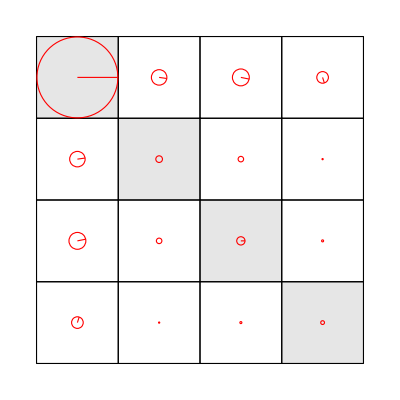
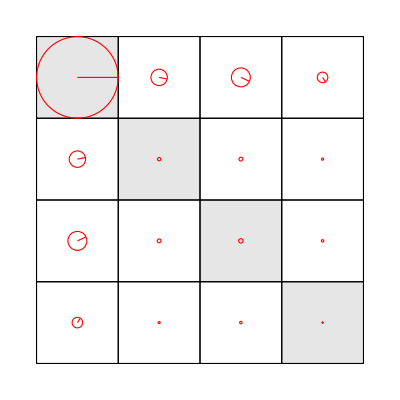
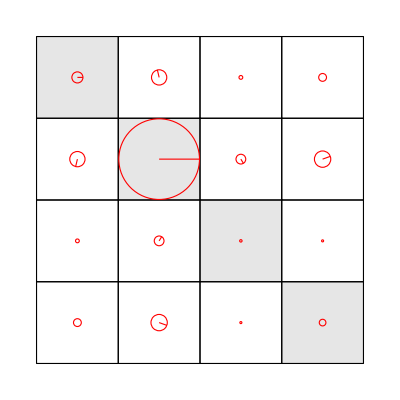
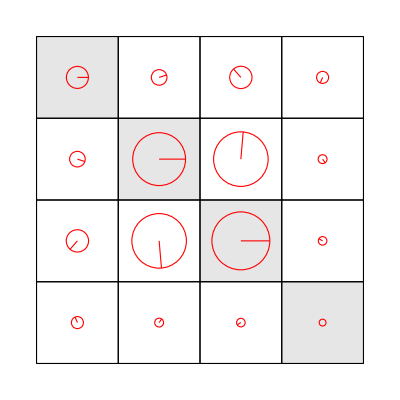
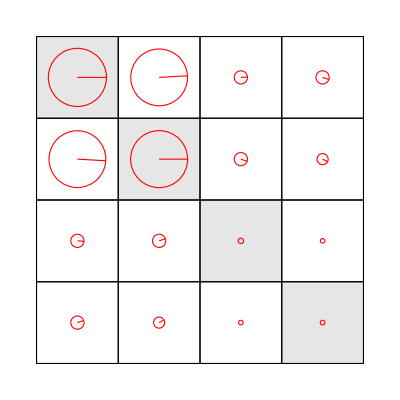
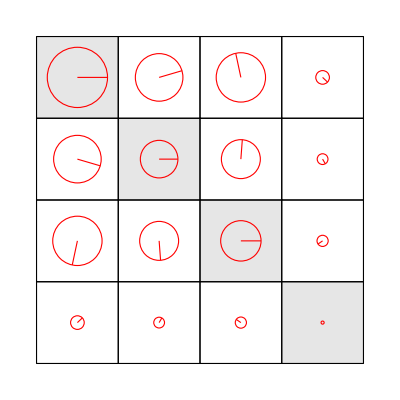
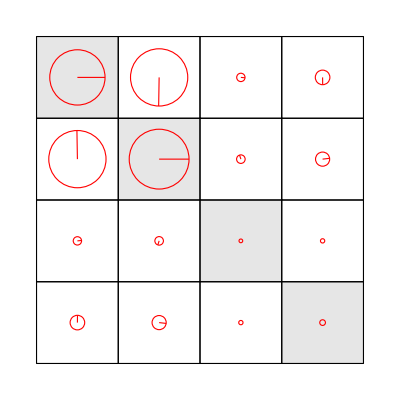
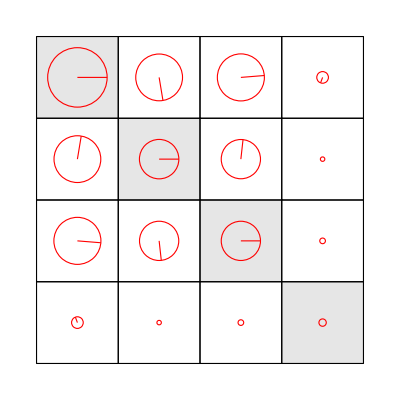

```mathematica
opts1b={borderDirectives->{Red,Thickness[0.002]},arrowDirectives->{Red,Thickness[0.002],Arrowheads[0]},fill2DShape->False,hide2DShapeSmallerThan->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&),frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&)};
GraphicsGrid[Map[complexMatrixDraw[#,opts1b]&,Transpose[myρs],{2}]]
```

#### Graph for fig 2

we are interested in the |10> initial state (i.e. index 5) and we truncate the matrix element at 1%

```mathematica
my2ρs=Transpose[myρs][[5]];
```

```mathematica
conc/@my2ρs
```

{Max[0,-2 Eigenvalues[{{0.0360752,0.00826523-0.00433037 ⅈ,0.0552441-0.00380989 ⅈ,0.0090625-0.0121061 ⅈ},{0.00826523+0.00433037 ⅈ,0.00410549,0.0325329+0.0124233 ⅈ,0.000730776-0.000862125 ⅈ},{0.0552441+0.00380989 ⅈ,0.0325329-0.0124233 ⅈ,0.948053,-0.0280588-0.00326534 ⅈ},{0.0090625+0.0121061 ⅈ,0.000730776+0.000862125 ⅈ,-0.0280588+0.00326534 ⅈ,0.0117662}}.KroneckerProduct[σy,σy].{{0.0360752,0.00826523+0.00433037 ⅈ,0.0552441+0.00380989 ⅈ,0.0090625+0.0121061 ⅈ},{0.00826523-0.00433037 ⅈ,0.00410549,0.0325329-0.0124233 ⅈ,0.000730776+0.000862125 ⅈ},{0.0552441-0.00380989 ⅈ,0.0325329+0.0124233 ⅈ,0.948053,-0.0280588+0.00326534 ⅈ},{0.0090625-0.0121061 ⅈ,0.000730776-0.000862125 ⅈ,-0.0280588-0.00326534 ⅈ,0.0117662}}.KroneckerProduct[σy,σy]]^2],Max[0,-2 Eigenvalues[{{0.0745696,-0.0352993+0.0639137 ⅈ,0.0386576+0.0265611 ⅈ,0.018933+0.0181288 ⅈ},{-0.0352993-0.0639137 ⅈ,0.501821,-0.0147672-0.451309 ⅈ,-0.0133294-0.0060295 ⅈ},{0.0386576-0.0265611 ⅈ,-0.0147672+0.451309 ⅈ,0.412654,-0.000538455-0.0169464 ⅈ},{0.018933-0.0181288 ⅈ,-0.0133294+0.0060295 ⅈ,-0.000538455+0.0169464 ⅈ,0.0109547}}.KroneckerProduct[σy,σy].{{0.0745696,-0.0352993-0.0639137 ⅈ,0.0386576-0.0265611 ⅈ,0.018933-0.0181288 ⅈ},{-0.0352993+0.0639137 ⅈ,0.501821,-0.0147672+0.451309 ⅈ,-0.0133294+0.0060295 ⅈ},{0.0386576+0.0265611 ⅈ,-0.0147672-0.451309 ⅈ,0.412654,-0.000538455+0.0169464 ⅈ},{0.018933+0.0181288 ⅈ,-0.0133294-0.0060295 ⅈ,-0.000538455-0.0169464 ⅈ,0.0109547}}.KroneckerProduct[σy,σy]]^2]}

{-Graphics-,-Graphics-}

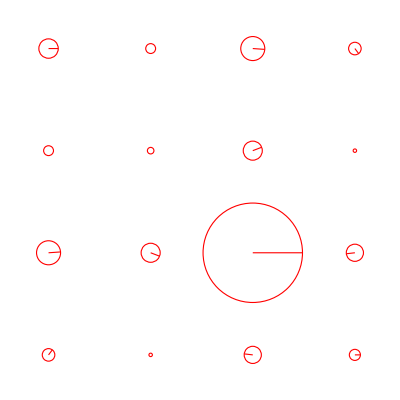
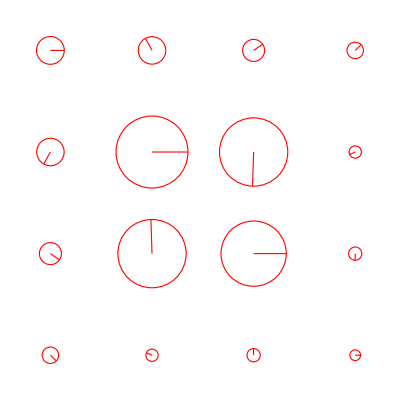

```mathematica
complexMatrixDraw[#,Sequence @@ opts1b]&/@my2ρs
tomoGraphs=complexMatrixDraw[#,Sequence @@ opts1b,showFrame->False]&/@Transpose[myρs][[5]]
```

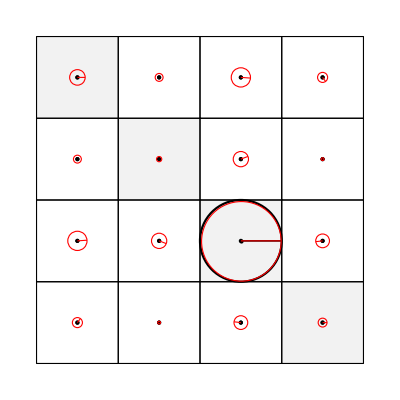
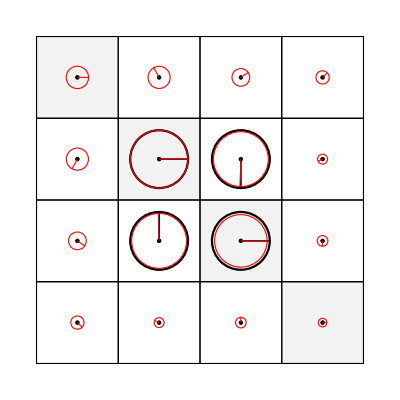

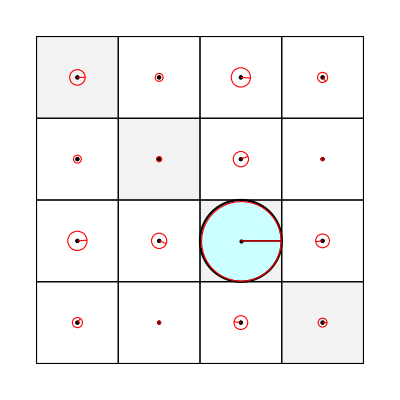
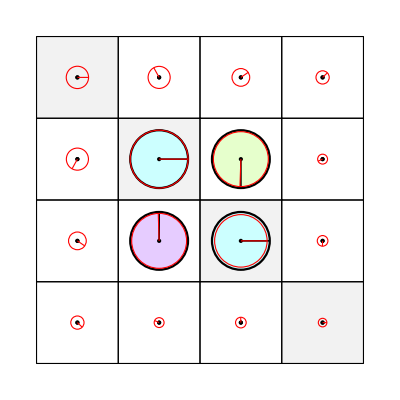

```mathematica
graphs=MapThread[Show[#1,#2]&,{idealGraphs,tomoGraphs}]
graphs=MapThread[Show[#1,#2]&,{idealGraphsb,tomoGraphs}]
```